```mathematica
Import["../EllipseFitting/vicon_input.m"]
Import["../PathPlanning/arm_motion.wl"]
```

```mathematica
jointangles={
ball1->{-0.143683,-1.64994,-2.0909,1.08001,1.27684,-0.820759,1.15413},
	ball2->{-0.291968,-1.63479,-2.11444,1.1337,1.2751,-0.778377,1.0817},
	ball3->{-0.462276,-1.64559,-2.0961,1.15458,1.27273,-0.685547,0.934875},
	ball4->{-0.580575,-1.66313,-2.07978,1.08256,1.27146,-0.653602,0.758463},
	ballstart->{-0.907861,-0.9862,-1.09998,2.29407,1.26024,-1.243,1.88064}
};
```

```mathematica
startConfig = jointangles[[5,2]];
endConfig = jointangles[[1,2]];
startPosW = Transpose[HomToCart3D[Transpose[{WAM7DOF[startConfig].{0,0,0,1}}]]][[1]];
endPosW =Transpose[HomToCart3D[Transpose[{WAM7DOF[endConfig].{0,0,0,1}}]]][[1]]; 
pathBallStartToEnd = LinearInterp[startConfig, endConfig = jointangles[[1,2]], 100];
```

```mathematica
pathEEPtsW = HomToCart3D[Transpose[WAMEEPtsFromConfigurationsW[pathBallStartToEnd]]];
pathEEPtsE = HomToCart3D[Transpose[WAMEEPtsFromConfigurationsE[pathBallStartToEnd]]];
```

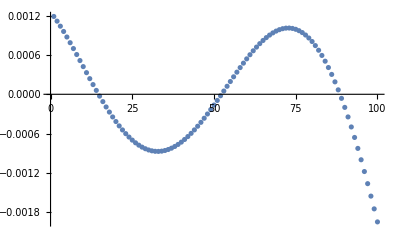

```mathematica
planeW = ComputePlane[Transpose[pathEEPtsW]];
planeNormalW = planeW[[2,2]];
planeRotW = RotationMatrix[{planeNormalW, {0,0,1}}];
planeWOff2D = planeRotW.pathEEPtsW;
Mean2DOff = Mean[planeWOff2D[[3]]];
planeWMeanOff2D = {planeWOff2D[[1]],planeWOff2D[[2]],ConstantArray[Mean2DOff, Dimensions[planeWOff2D][[2]]]};
planeOffsetW = planeWOff2D[[3]] - planeWMeanOff2D[[3]];
ListPlot[planeOffsetW]
```

```mathematica
pathLine = Line[{startPosW, endPosW}];
Manipulate[
Show[
{
ShowWAMPose[pathBallStartToEnd[[curPos]], -1, 1],
ListPointPlot3D[{startPosW, endPosW}],
ListPointPlot3D[Transpose[pathEEPtsW]],
ListPointPlot3D[Transpose[pathEEPtsE]],
Graphics3D[{Red,pathLine}]
}], {curPos,1,100, 1}]
```

```mathematica
Dimensions[pathBallStartToEnd][[1]]
```

101

```mathematica
ikConfigA = SillyIK[startPosW];
ikConfigB = SillyIK[endPosW];
linearVect = endPosW - startPosW;
linearDist = Norm[linearVect]
(*linearVectN = linearVect / linearDist;*)
nSlices = 5;
(*linearSliceSize = linearDist / nSlices;*)
linearSlice = linearVect / nSlices;
linearPts = {};
For[lpi = 0, lpi ≤ nSlices, lpi++, AppendTo[linearPts, startPosW + linearSlice * lpi]]
linearPathConfigs = {};
For[lpi = 0, lpi ≤ nSlices, lpi++, AppendTo[linearPathConfigs,SillyIK[linearPts[[lpi+1]]]]]
```

0.67751

```mathematica
Manipulate[
Show[{
ShowWAMPose[ikConfigA[[2]], -1, 1],
ShowWAMPose[ikConfigB[[2]], -1, 1],
ShowWAMPose[linearPathConfigs[[pathPtNo,2]], -1, 1],
ListPointPlot3D[linearPts]}], {pathPtNo, 1,nSlices+1,1}]
```

Part::partd: Part specification ikConfigA⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of ikConfigA⟦2⟧ does not exist.

Part::partw: Part 4 of ikConfigA⟦2⟧ does not exist.

Part::partw: Part 5 of ikConfigA⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification ikConfigB⟦2⟧ is longer than depth of object.

Part::partd: Part specification linearPathConfigs⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPointPlot3D::arrayerr: linearPts must be a valid array or a list of valid arrays.

Show::gcomb: Could not combine the graphics objects in Show[{,,,ListPointPlot3D[linearPts]}].

Part::partw: Part 2 of SillyIK[{-0.412088,0.0163352,0.295682}] does not exist.

Part::partw: Part 3 of SillyIK[{-0.412088,0.0163352,0.295682}]⟦2⟧ does not exist.

Part::partw: Part 4 of SillyIK[{-0.412088,0.0163352,0.295682}]⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[Transpose[{}]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[Transpose[Transpose[{}]],AspectRatio→1,PlotRange→{{-1,1},{-1,1},{-1,1}}],}].

Show::gcomb: Could not combine the graphics objects in Show[{,,Show[{ListPointPlot3D[Transpose[Transpose[{}]],AspectRatio→1,PlotRange→{{«2»},{«2»},{«2»}}],}],}].

```mathematica
SillyIK[linearPts[[5]]]
```

{{2.52196×10^-11,{testTheta1→-0.109153,testTheta2→-1.46988,testTheta3→0.700422,testTheta4→-1.19922,testTheta5→-0.231334,testTheta6→0.609372}},{-0.109153,-1.46988,0.700422,-1.19922,-0.231334,0.609372,0}}

```mathematica
linearPathConfigs[[1,2]]
```

{0.0290651,-0.338859,-0.0796368,-1.83792,0.897999,0.11026,0}

```mathematica
(*NMinimize[Norm[Transpose[-inPt],{testTheta1, testTheta2, testTheta3, testTheta4, testTheta5, testTheta6}];*)
```

```mathematica
SimpleThirdOrder[inConstVar_, inVar1_, inVar2_, inVar3_, inMultiplier_]:= inConstVar + inMultiplier * inVar1 + inMultiplier^2 * inVar2 + inMultiplier^3 * inVar3
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0.5]
```

0.5 testTheta1A+0.25 testTheta1B+0.125 testTheta1C+testTheta1Z

```mathematica
pathSol = NMinimize[
Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 0],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 0],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 0],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 0],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 0]
}
]][[1]]-linearPts[[1]]]+

Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0.2],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 0.2],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 0.2],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 0.2],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 0.2],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 0.2]
}
]][[1]]-linearPts[[2]]]+

Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0.4],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 0.4],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 0.4],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 0.4],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 0.4],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 0.4]
}
]][[1]]-linearPts[[3]]]+

Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0.6],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 0.6],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 0.6],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 0.6],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 0.6],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 0.6]
}
]][[1]]-linearPts[[4]]]+

Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 0.8],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 0.8],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 0.8],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 0.8],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 0.8],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 0.8]
}
]][[1]]-linearPts[[5]]]+

Norm[Transpose[WAM7DOFCartW[
{
SimpleThirdOrder[testTheta1Z, testTheta1A, testTheta1B, testTheta1C, 1.0],
SimpleThirdOrder[testTheta2Z, testTheta2A, testTheta2B, testTheta2C, 1.0],
SimpleThirdOrder[testTheta3Z, testTheta3A, testTheta3B, testTheta3C, 1.0],
SimpleThirdOrder[testTheta4Z, testTheta4A, testTheta4B, testTheta4C, 1.0],
SimpleThirdOrder[testTheta5Z, testTheta5A, testTheta5B, testTheta5C, 1.0],
SimpleThirdOrder[testTheta6Z, testTheta6A, testTheta6B, testTheta6C, 1.0]
}
]][[1]]-linearPts[[6]]]
,{
testTheta1Z,testTheta1A,testTheta1B,testTheta1C,
testTheta2Z,testTheta2A,testTheta2B,testTheta2C,
testTheta3Z,testTheta3A,testTheta3B,testTheta3C,
testTheta4Z,testTheta4A,testTheta4B,testTheta4C,
testTheta5Z,testTheta5A,testTheta5B,testTheta5C,
testTheta6Z,testTheta6A,testTheta6B,testTheta6C
}]
```

{0.00644277,{testTheta1Z→0.0883861,testTheta1A→-0.0654681,testTheta1B→-0.194729,testTheta1C→0.271692,testTheta2Z→-0.339757,testTheta2A→-1.34316,testTheta2B→0.179552,testTheta2C→-0.122576,testTheta3Z→-0.183168,testTheta3A→0.582854,testTheta3B→0.223514,testTheta3C→-0.337423,testTheta4Z→-1.82475,testTheta4A→0.00916884,testTheta4B→0.92084,testTheta4C→0.207334,testTheta5Z→0.515237,testTheta5A→0.919604,testTheta5B→-0.559567,testTheta5C→0.0559581,testTheta6Z→-0.0179602,testTheta6A→-0.146735,testTheta6B→0.315195,testTheta6C→-0.282885}}

```mathematica
pathSol[[2]]
pathSol[[2,12]]
```

{testTheta1Z→0.0883861,testTheta1A→-0.0654681,testTheta1B→-0.194729,testTheta1C→0.271692,testTheta2Z→-0.339757,testTheta2A→-1.34316,testTheta2B→0.179552,testTheta2C→-0.122576,testTheta3Z→-0.183168,testTheta3A→0.582854,testTheta3B→0.223514,testTheta3C→-0.337423,testTheta4Z→-1.82475,testTheta4A→0.00916884,testTheta4B→0.92084,testTheta4C→0.207334,testTheta5Z→0.515237,testTheta5A→0.919604,testTheta5B→-0.559567,testTheta5C→0.0559581,testTheta6Z→-0.0179602,testTheta6A→-0.146735,testTheta6B→0.315195,testTheta6C→-0.282885}

testTheta3C→-0.337423

```mathematica
Manipulate[
Show[{
ShowWAMPose[ikConfigA[[2]], -1, 1],
ShowWAMPose[ikConfigB[[2]], -1, 1],

ShowWAMPose[
{
SimpleThirdOrder[pathSol[[2,1,2]], pathSol[[2,2,2]], pathSol[[2,3,2]], pathSol[[2,4,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,5,2]], pathSol[[2,6,2]], pathSol[[2,7,2]], pathSol[[2,8,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,9,2]], pathSol[[2,10,2]], pathSol[[2,11,2]], pathSol[[2,12,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,13,2]], pathSol[[2,14,2]], pathSol[[2,15,2]], pathSol[[2,16,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,17,2]], pathSol[[2,18,2]], pathSol[[2,19,2]], pathSol[[2,20,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,21,2]], pathSol[[2,22,2]], pathSol[[2,23,2]], pathSol[[2,24,2]], pathSlider],
0
}
, -1, 1],

ListPointPlot3D[linearPts]}], {pathSlider, 0, 1}]
```

```mathematica
reachMajorOrientation=(endPosW - startPosW);
reachMidPtAlongLine = reachMajorOrientation / 2 + startPosW;
reachNorm = Norm[reachMajorOrientation]
ParametricEllipse2DPtAtZZero[inTheta_, inA_, inB_]:={inA * Cos[inTheta], inB * Sin[inTheta], 0}
parametric3DEllipse = RotationMatrix[{{0,0,1}, reachMajorOrientation/reachNorm}].ParametricEllipse2DPtAtZZero[parametricTheta, reachNorm, reachNorm / 2]
```

0.67751

{0.+0.424906 Cos[parametricTheta]-0.180314 Sin[parametricTheta],0.+0.360627 Cos[parametricTheta]-0.0813319 Sin[parametricTheta],0.-0.385256 Cos[parametricTheta]-0.275004 Sin[parametricTheta]}

```mathematica
Manipulate[
Show[{
ShowWAMPose[ikConfigA[[2]], -1, 1],
ShowWAMPose[ikConfigB[[2]], -1, 1],

ShowWAMPose[
{
SimpleThirdOrder[pathSol[[2,1,2]], pathSol[[2,2,2]], pathSol[[2,3,2]], pathSol[[2,4,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,5,2]], pathSol[[2,6,2]], pathSol[[2,7,2]], pathSol[[2,8,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,9,2]], pathSol[[2,10,2]], pathSol[[2,11,2]], pathSol[[2,12,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,13,2]], pathSol[[2,14,2]], pathSol[[2,15,2]], pathSol[[2,16,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,17,2]], pathSol[[2,18,2]], pathSol[[2,19,2]], pathSol[[2,20,2]], pathSlider],
SimpleThirdOrder[pathSol[[2,21,2]], pathSol[[2,22,2]], pathSol[[2,23,2]], pathSol[[2,24,2]], pathSlider],
0
}
, -1, 1],
ListPointPlot3D[linearPts],
ParametricPlot3D[parametric3DEllipse, {parametricTheta, -Pi, Pi}]
}

], {pathSlider, 0, 1}]
```